```mathematica
Quit[];
```

```mathematica
path[{x1_,y1_},{x2_,y2_}]:=If[x1-x2 ==0(*to prevent 1/0 exception*),x-x1==0
(*If x1=x2, then the equation of line is x= x1=x2 *),((y1-y2)/(x1-x2)x)-y+(y1-(x1*(y1-y2)/(x1-x2)))==0(*This is the equation of line between two points {x1,y1} and {x2,y2}*)];(*A function to find the equation of the line between points {x1,y1} and {x2,y2} *)
collision[{r_,x0_,y0_},{x1_,y1_},{x2_,y2_}]:=(*Function to determine whether the path between nodes {x1,y1} and {x2,y2} does not leads to a collision with circular obstacle {radius,x,y} *)If[
(*If the solution returns two roots, then it means the path leads to collision, If it returns only one root, the path grazes the obstacle, no root, the path is clear of the obstacle*)
Length[
Values[
Solve[{(x-x0)^2+(y-y0)^2-r^2 ==0,path[{x1,y1},{x2,y2}],x1<=x≤x2 || x2<=x≤x1,y1<=y≤y2 || y2≤y≤y1},{x,y},Reals]
(*The equation of the circel and the line of the path are solve between the limits, {x1,y1} and {x2,y2}*)
](*Values indicates the number of roots*)
]>1|| ((x1-x0)^2+(y1-y0)^2<r^2)||((x2-x0)^2+(y2-y0)^2<r^2)(*These conditions check whether any of the node lie inside the circular obstacle*)
,True,False];
```

```mathematica
neighbours[nodes_,currentNode_,obstacles_](*Returns all the nodes which can form an edge without resulting in collision with any of the circular obstacles*):=
Module[{neighbourNodes},
neighbourNodes = nodes;
neighbourNodes = Delete[neighbourNodes, Position[neighbourNodes,currentNode] [[1]]  ];
temp = neighbourNodes;
For[i=1,i≤Length[neighbourNodes],i++,
For[j=1,j≤Length[obstacles],j++,

If[
collision[obstacles[[j]],neighbourNodes[[i]],currentNode ],
If[MemberQ[temp,neighbourNodes[[i]]],
temp =Delete[temp, Position[temp,neighbourNodes[[i]]][[1]]   ];

];
];

];
];
neighbourNodes = temp;
Return[neighbourNodes ];
];
```

```mathematica
heuristicCostEstimate[{x1_,y1_},{x2_,y2_}]:=√((x1-x2)^2+(y1-y2)^2);(*function returns the distance between the nodes,{x1,y1}and {x2,y2} *)


Astar[rdsrbt_,obstcl_,positions_,{start_,goal_}]:= 
Module[
{closedSet},
{crclrobstcl};
crclrobstcl = {};
nodePositions = positions;
If[MemberQ[nodePositions,start],nodePositions = Delete[nodePositions,Position[nodePositions,start][[1]] ];];(*deletes start from the set of nodes if duplicated*)
If[MemberQ[nodePositions,goal],nodePositions = Delete[nodePositions,Position[nodePositions,goal][[1]] ];];
(*deletes goal from the set of nodes if duplicated*)
For[c=1,c≤Length[obstcl],c++,
crclrobstcl = Append[crclrobstcl, (  obstcl[[c]]+{rdsrbt,0,0}    )     ];
];(*Obstacle radius is enlarged by robot radius*)

closedSet = {};(*Set of nodes already evaluated*)

nodes =Join[{start},nodePositions,{goal}];(*List of all nodes with the starting node at the beginning and the goal at the end*)
position = 1;(*Position of the node*)
gscore=2;(*gscore of the node( distance travelled from Start to the node using the shortest path)*)
fscore = 3;(*Sum of gscore and distance between the node and the goal*)
camefrom = 4;(*Map of navigated nodes*)
 nodedata = {{nodes[[1]],{},{},{}}};(*Node data is an object representing a node with structure {position({x,y}),{gscore},{hscore},{came_from}}*)
For[i=2,i<=Length[nodes],i++,
nodedata = Append[nodedata,{nodes[[i]],{},{},{}}];
];(*getting nodedata objects for all nodes*)
startPos = 1;
goalPos = Length[nodes];
nodedata[[startPos]][[gscore]] = 0;(*Cost from start along the best known path*)
nodedata[[startPos]][[fscore]] =nodedata[[startPos]][[gscore]]+heuristicCostEstimate[nodedata[[startPos]][[position]],nodedata[[goalPos]][[position]]];
(*Estimated total cost from start to goal*)
openSet = {nodedata[[startPos]]};(*Set of tentative nodes to  be evaluated*)
While[
Length[openSet]>0,

current =Sort[openSet,    #1[[fscore]]  <  #2[[fscore]]   &] (*sorting node date in ascending order with respect to fscore (with exceptions to avoid nodes with empty fcores(whose fscore is not yet calculated) ) and the first element of this sorted list is taken to obtain the node with minimum fscore value  *) [[1]];


If[current[[position]] == nodedata[[goalPos]][[position]],
Return[                 Join[current[[camefrom]],{current[[position]]}     ]   ]                                                   ];
openSet =Delete[ openSet,Position[openSet,current][[1]]  ];(*start node will be the first current and it is removed from openset*)
closedSet =Append[closedSet,current];(*start node is added to closed set*)

neighbourNodes =  neighbours[nodes,current[[position]],crclrobstcl];(*neighbour nodes to current are found*)
nghbr = {};

For[i=1,i≤Length[neighbourNodes],i++,
For[j=1,j≤Length[nodedata],j++,
If[neighbourNodes[[i]] == nodedata[[j]][[position]], nghbr = Append[nghbr,nodedata[[j]]]  ];
];
];
neighbourNodes = nghbr;(*all the neighbour nodes are converted to the required format*)
For[i=1,i≤Length[ neighbourNodes ],i++,


If[MemberQ[closedSet,   neighbourNodes[[i]] ] ,Continue[]; ];(*If neighbour is a member of closed set, continue *)

tentativeGscore = current[[gscore]]+ heuristicCostEstimate[current[[position]],neighbourNodes[[i]][[position]]   ];(*Tentative gscore is calculated for the neighbournode through current*)


If[!MemberQ[openSet,neighbourNodes[[i]]],


neighbourNodes[[i]][[camefrom]]= Append[Join[neighbourNodes[[i]][[camefrom]],  current[[camefrom]]        ],current[[position]]  ]     ;

neighbourNodes[[i]][[gscore]] = tentativeGscore;

neighbourNodes[[i]][[fscore]] =  neighbourNodes[[i]][[gscore]] + heuristicCostEstimate[  neighbourNodes[[i]][[position]],nodedata[[goalPos]][[position]]        ];
openSet = Append[openSet,neighbourNodes[[i]]];


,


If[tentativeGscore<neighbourNodes[[i]][[gscore]],
neighbourNodes[[i]][[camefrom]]= Append[Join[neighbourNodes[[i]][[camefrom]],  current[[camefrom]]        ],current[[position]]  ]     ;
neighbourNodes[[i]][[gscore]] = tentativeGscore;
neighbourNodes[[i]][[fscore]] =  neighbourNodes[[i]][[gscore]] + heuristicCostEstimate[  neighbourNodes[[i]][[position]],nodedata[[goalPos]][[position]]        ];



];
];
];



For[i=1,i≤Length[neighbourNodes],i++,
For[j=1,j≤Length[nodedata],j++,
If[neighbourNodes[[i]] == nodedata[[j]][[position]], nodedata[[j]] = neighbourNodes[[i]] ];
];
];(*changes in neighbour nodes are reflected in nodedata*)

For[i=1,i≤Length[neighbourNodes],i++,
For[j=1,j≤Length[openSet],j++,
If[neighbourNodes[[i]] == openSet[[j]][[position]], openSet[[j]] = neighbourNodes[[i]] ];
];
];



(*changes in neighbour nodes are reflected in openset*)



];

Return["Failure"]

];


formatChangeCircle[{r_,x_,y_}]:= Disk[{x,y},r];

graphAstar[rdsrbt_,obstcl_,nodePositions_,{start_,goal_}]:=
Module[{crclrobstcl},
crclrobstcl = {};
For[c=1,c≤Length[obstcl],c++,
crclrobstcl = Append[crclrobstcl, (  obstcl[[c]]+{rdsrbt,0,0}    )     ];
];(*Obstacle radius is enlarged by robot radius*)

v1 =Graphics[{Line[{{5,0},{-5,0}}],Line[{{0,5},{0,-5}}],    (*X and Y axis*)
Purple,Map[formatChangeCircle,crclrobstcl],(*enlarged obstacles*)
Gray,Map[formatChangeCircle,obstcl],
Brown,PointSize-> 0.025,Point[nodePositions],Blue,Point[{start}],Green,Point[{goal}],
Red,Map[Line,edgesPossible[rdsrbt,crclrobstcl,nodePositions,{start,goal}]],
Thick,Black,Line[Astar[rdsrbt,obstcl,nodePositions,{start,goal}]]  
}];
Return[Show[v1]]
];


edgesPossible[rdsrbt_,crclrobstcl_,nodePositions_,{start_,goal_}]:=
Module[{allEdges},
temp1 = {};

allNodes = Join[{start},nodePositions,{goal}];

For[ g=1,g<=Length[allNodes],g++,

nghbrs = neighbours[allNodes,allNodes[[g]],crclrobstcl];

For[h=1,h<=Length[  nghbrs  ], h++,
temp1 =Join[temp1,{{   allNodes[[g]],nghbrs[[h]]   }    } ];

];

];
allEdges = temp1;
Return[allEdges]
];
```

```mathematica
(*The function Astar returns the nodes of the optimum path*)
(*the input for this function is Astar[radius_of_robot,{obst1,obst2,..},{node1,node2,...},{start_node,goal}]
where obst is form {radius,x,y}
      node,start and goal are of form {x,y} is of f*)
Astar[2,{{4,30,30},{6,37,62},{5,37,75},{3,50,62},{4,62,50}},{{25,25},{25,50},{25,75},{50,25},{50,50},{50,75},{75,25},{75,50},{75,75}},{{25,75},{50,75}}]
```

{{25,75},{25,50},{50,50},{75,75},{50,75}}

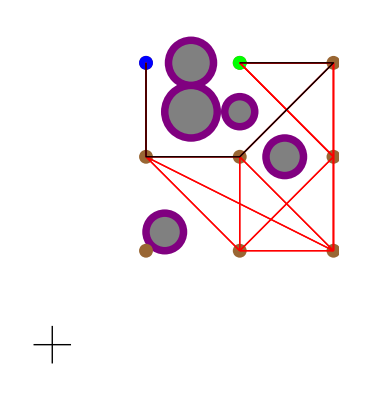

```mathematica
(*The function graphAstar returns a graphical representation of the function Astar mentioned above, its syntax is the same as that of Astar function mentioned above.*)
(*The blue node is the start node the green one is the goal and the black path is the optimum path. The grey circles are the obstacles and the purple extensions of the obstacles compensate for the size and shape of the robot*)
graphAstar[2,{{4,30,30},{6,37,62},{5,37,75},{3,50,62},{4,62,50}},{{25,25},{25,50},{25,75},{50,25},{50,50},{50,75},{75,25},{75,50},{75,75}},{{25,75},{50,75}}]
```